```mathematica
(* Created by Francisco Torrenti - June 2022 *)
```

```mathematica
(*This notebook reads the output data generated by CosmoLattice (in text format) and creates a series of useful figures. *)
```

```mathematica
Clear["Global`*"] 
(*Clears all variables*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*Sets working directory to current directory*)
```

```mathematica
strm=OpenRead["average_scale_factor.txt"];  (*Opens file to read data from*)
(*Skip[strm,String,1];*)  (* If you add headers to the text files, uncomment this to skip the first line *)
NumColumns=4;  (*Number of columns in file*)
scale=ReadList[strm,Table[Number,{NumColumns}]];  (*Reads data and creates table*)
```

```mathematica
FinalTime=scale[[Length[scale]]][[1]];  (*Final time of simulation*)
```

## GW Spectra outputs

```mathematica
(* Parameters from the simulation *)
  Npoints=64;   (* N: number of lattice points per side *)
  tOutputInfreq=10;  (* time interval between spectra *)
  NumBins=IntegerPart[Sqrt[3]* Npoints/2]; (* number of bins in the spectra *)

(* Parameters for spectra output *)
  s3=1; (* frequency of spectra output. Spectra printed are s3*n+1 for n=1, 2,... *)
```

```mathematica
(*Number of spectra to be printed*)
NumSpectra=FinalTime/(tOutputInfreq*s3)
```

149.

```mathematica
colors=Table[ColorData["Rainbow", t],{t,1,0,-1/NumSpectra}]; (*creates a rainbow of colours for spectra figures*)
```

```mathematica
specTimes=Table[tOutputInfreq*s3*(i-1),{i,1,NumSpectra*s3}]; (*approximate spectra times*)
```

```mathematica
NumColumns=3;
specGWs=ReadList["spectra_gws.txt",Table[Number,{NumColumns}]];
```

```mathematica
Table[
spectraGWs[i]=Table[{specGWs[[j]][[1]],specGWs[[j]][[2]]},{j,NumBins*s3*(i-1) + 1,NumBins*s3*(i-1)+NumBins}],{i,1,NumSpectra}];
```

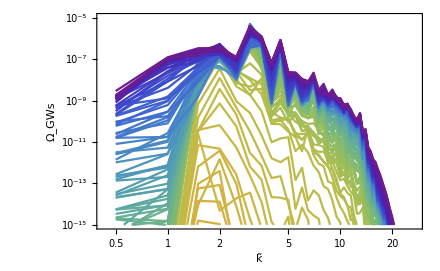

```mathematica
ListLogLogPlot[Table[spectraGWs[i],{i,1,NumSpectra}],PlotStyle->colors,Joined->True,PlotRange->{10^-15,10^-5},ImageSize->440,Frame -> True,FrameLabel->{Style["k̃",FontSize->14,Black],Style["Ω_GWs",FontSize->14,Black]},FrameTicksStyle->Directive[Black,14]]
```

```mathematica
EnergyGWs=OpenRead["energy_gws.txt"];  (*Opens file to read data from*)
(*Skip[strm,String,1];*)  (* If you add headers to the text files, uncomment this to skip the first line *)
NumColumns=3;  (*Number of columns in file*)
EGWs=ReadList[EnergyGWs,Table[Number,{NumColumns}]];  (*Reads data and creates table*)
```

```mathematica
ΩGW=Interpolation[Table[{EGWs[[i,1]],EGWs[[i,2]]},{i,1,Length[EGWs]}]];
```

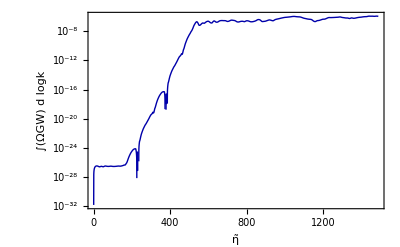

```mathematica
LogPlot[ΩGW[t],{t,0,FinalTime},ImageSize->400,
PlotStyle->{{Thick,Darker[Blue]}},Frame->True,PlotRange->All,FrameLabel->{Style[η̃,FontSize->16,Black],Style["∫(ΩGW) d logk",FontSize->16,Black]},FrameTicksStyle->Directive[Black,14]
]
```

```mathematica
ρGW=Interpolation[Table[{EGWs[[i,1]],EGWs[[i,3]]},{i,1,Length[EGWs]}]];
```

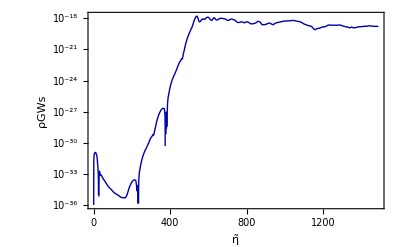

```mathematica
LogPlot[ρGW[t],{t,0,FinalTime},ImageSize->400,
PlotStyle->{{Thick,Darker[Blue]}},Frame->True,PlotRange->All,FrameLabel->{Style[η̃,FontSize->16,Black],Style["ρGWs",FontSize->16,Black]},FrameTicksStyle->Directive[Black,14]
]
```